# Игра “Жизнь”

## Интегрированные математические пакеты

Юдинцев В. В.

Кафедра теоретической механики. Самарский университет.

## Функции

### Пример колонии “Глайдер”

Колонию будет задавать списком пар координат "живых" клеток . Например, колония "Глайдер" может быть представлена списком :

```mathematica
colony={{0,0},{1,0},{2,0},{2,1},{1,2}};
```

Построим изображение этой колонии при помои функции ListPlot.

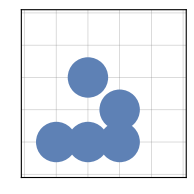

```mathematica
ListPlot[colony,PlotStyle->PointSize[0.15],PlotRange->{{-1,4},{-1,4}},AspectRatio->1,
Frame->True,GridLines->{Range[-1,4]},FrameTicks->None]
```

### Функция определяет принадлежность клетки колонии

Для проверки принадлежности клетки x колонии col можно использовать функцию MemberQ, которая возвращает True если элемент, указанный вторым аргументом, будет принадлежать списку, указанному первым аргументом. Для рассматриваемого примера колонии:

```mathematica
MemberQ[colony,{1,0}]
```

True

```mathematica
MemberQ[colony,{5,0}]
```

False

### Список смежных клеток (занятых или пустых), включая саму клетку

Для определения количества соседей у некоторой клетки с координатами c = (x, y) необходимо определить список смежных клеток (клеток - соседей) и подсчитать в этом списке количество клеток, которые принадлежат колонии.

```mathematica
Tuples[{{1,2},{3,4,5}}]
```

{{1,3},{1,4},{1,5},{2,3},{2,4},{2,5}}

Список смещений координат

```mathematica
Tuples[{{-1,0,1},{-1,0,1}}]
```

{{-1,-1},{-1,0},{-1,1},{0,-1},{0,0},{0,1},{1,-1},{1,0},{1,1}}

```mathematica
Tuples[{-1,0,1},2]
```

{{-1,-1},{-1,0},{-1,1},{0,-1},{0,0},{0,1},{1,-1},{1,0},{1,1}}

```mathematica
DeleteCases[Tuples[{-1,0,1},2],{0,0}]
```

{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}

```mathematica
{2,3}+#&/@DeleteCases[Tuples[{-1,0,1},2],{0,0}]
```

{{1,2},{1,3},{1,4},{2,2},{2,4},{3,2},{3,3},{3,4}}

Координаты смежных клеток для {2,3}

```mathematica
{x,y}+#&/@DeleteCases[Tuples[{-1,0,1},2],{0,0}]
```

{{-1+x,-1+y},{-1+x,y},{-1+x,1+y},{x,-1+y},{x,1+y},{1+x,-1+y},{1+x,y},{1+x,1+y}}

Какие из них принадлежат колонии

```mathematica
MemberQ[colony,{2,3}+#]&/@DeleteCases[Tuples[{-1,0,1},2],{0,0}]
```

{True,False,False,False,False,False,False,False}

### Функции вычисления количества соседей

```mathematica
countNeighbours[x_,colony_]:=Count[MemberQ[colony,x+#]&/@DeleteCases[Tuples[{-1,0,1},2],{0,0}],True];
```

```mathematica
countNeighbours[{1,1},colony]
```

5

### Определение ареала колонии

```mathematica
Outer[f,{a,b},{c,d,e}]
```

{{f[a,c],f[a,d],f[a,e]},{f[b,c],f[b,d],f[b,e]}}

```mathematica
Outer[f,{{1,2},{3,4}},{{10,20}}]
```

{{{{f[1,10],f[1,20]}},{{f[2,10],f[2,20]}}},{{{f[3,10],f[3,20]}},{{f[4,10],f[4,20]}}}}

```mathematica
Outer[f,{{1,2},{3,4}},{{10,20}},1]
```

{{f[{1,2},{10,20}]},{f[{3,4},{10,20}]}}

```mathematica
Flatten[Outer[f,{{1,2},{3,4}},{{10,20}},1]]
```

{f[{1,2},{10,20}],f[{3,4},{10,20}]}

```mathematica
Outer[#1+#2&,colony,Tuples[{-1,0,1},2],1]
Flatten[%,1]
Union[%]
```

{{{-1,-1},{-1,0},{-1,1},{0,-1},{0,0},{0,1},{1,-1},{1,0},{1,1}},{{0,-1},{0,0},{0,1},{1,-1},{1,0},{1,1},{2,-1},{2,0},{2,1}},{{1,-1},{1,0},{1,1},{2,-1},{2,0},{2,1},{3,-1},{3,0},{3,1}},{{1,0},{1,1},{1,2},{2,0},{2,1},{2,2},{3,0},{3,1},{3,2}},{{0,1},{0,2},{0,3},{1,1},{1,2},{1,3},{2,1},{2,2},{2,3}}}

{{-1,-1},{-1,0},{-1,1},{0,-1},{0,0},{0,1},{1,-1},{1,0},{1,1},{0,-1},{0,0},{0,1},{1,-1},{1,0},{1,1},{2,-1},{2,0},{2,1},{1,-1},{1,0},{1,1},{2,-1},{2,0},{2,1},{3,-1},{3,0},{3,1},{1,0},{1,1},{1,2},{2,0},{2,1},{2,2},{3,0},{3,1},{3,2},{0,1},{0,2},{0,3},{1,1},{1,2},{1,3},{2,1},{2,2},{2,3}}

{{-1,-1},{-1,0},{-1,1},{0,-1},{0,0},{0,1},{0,2},{0,3},{1,-1},{1,0},{1,1},{1,2},{1,3},{2,-1},{2,0},{2,1},{2,2},{2,3},{3,-1},{3,0},{3,1},{3,2}}

```mathematica
colonyArea[colony_]:=Union[Flatten[Outer[#1+#2&,colony,Tuples[{-1,0,1},2],1],1]];
```

### Функция вычисления следующего поколения

```mathematica
{#,countNeighbours[#,colony],MemberQ[colony,#]}&/@colonyArea[colony]
```

{{{-1,-1},1,False},{{-1,0},1,False},{{-1,1},1,False},{{0,-1},2,False},{{0,0},1,True},{{0,1},3,False},{{0,2},1,False},{{0,3},1,False},{{1,-1},3,False},{{1,0},3,True},{{1,1},5,False},{{1,2},1,True},{{1,3},1,False},{{2,-1},2,False},{{2,0},2,True},{{2,1},3,True},{{2,2},2,False},{{2,3},1,False},{{3,-4},1,False},{{3,-3},2,False},{{3,-2},3,False},{{3,-1},3,False},{{3,0},3,False},{{3,1},2,False},{{3,2},1,False},{{4,-4},1,False},{{4,-3},1,True},{{4,-2},2,True},{{4,-1},1,True},{{4,0},1,False},{{5,-4},1,False},{{5,-3},2,False},{{5,-2},3,False},{{5,-1},2,False},{{5,0},1,False}}

```mathematica
nextGeneration[colony_]:=#[[1]]&/@Select[{#,countNeighbours[#,colony],MemberQ[colony,#]}&/@colonyArea[colony],
#[[2]]==3||(#[[2]]==2&&#[[3]])&]
```

## Формирование массива поколений

Для формирования списка поколений используем функции Nest и NestList. Функция Nest возвращает результат применения функции к аргументу заданное количество раз.

```mathematica
Nest[f,x,4]
```

f[f[f[f[x]]]]

Функция NestList[f, x, n] формирует список результатов применения функции f к выражению x от  0 до n раз :

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

Четыре поколения колонии “Глайдер”:

```mathematica
NestList[nextGeneration,colony,4]
```

{{{0,0},{1,0},{2,0},{2,1},{1,2}},{{0,1},{1,-1},{1,0},{2,0},{2,1}},{{0,0},{1,-1},{2,-1},{2,0},{2,1}},{{1,-1},{1,1},{2,-1},{2,0},{3,0}},{{1,-1},{2,-1},{2,1},{3,-1},{3,0}}}

## Весь код

```mathematica
countNeighbours[x_,colony_]:=Count[MemberQ[colony,x+#]&/@DeleteCases[Tuples[{-1,0,1},2],{0,0}],True];
colonyArea[colony_]:=Union[Flatten[Outer[#1+#2&,colony,Tuples[{-1,0,1},2],1],1]];
nextGeneration[colony_]:=#[[1]]&/@Select[{#,countNeighbours[#,colony],MemberQ[colony,#]}&/@colonyArea[colony],
#[[2]]==3||(#[[2]]==2&&#[[3]])&]
```

## Глайдер

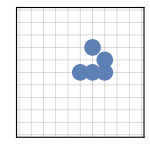
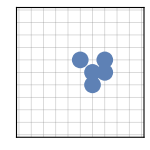
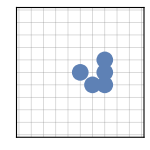
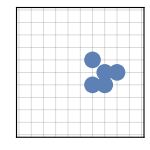
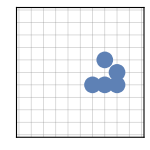

```mathematica
colony={{0,0},{1,0},{2,0},{2,1},{1,2}};
NestList[nextGeneration,colony,5];
ListPlot[%[[#]],PlotStyle->PointSize[0.08],PlotRange->{{-5,5},{-5,5}},AspectRatio->1,Axes->False,Frame->True,FrameTicks->None,GridLines->{Range[-5,5]},ImageSize->150]&/@Range[5]
```

## Ее один пример

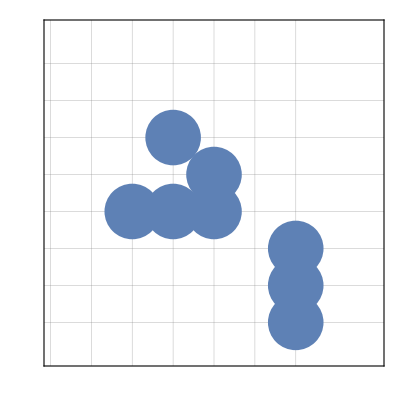

```mathematica
colony={{0,0},{1,0},{2,0},{2,1},{1,2},{4,-1},{4,-2},{4,-3}};
ListPlot[colony,PlotStyle->PointSize[0.1],PlotRange->{{-2,6},{-4,5}},AspectRatio->1,
Frame->True,Axes->False,GridLines->{Range[-3,4]},FrameTicks->None]
```

```mathematica
NestList[nextGeneration,colony,100];
Animate[ListPlot[%[[i]],PlotStyle->PointSize[0.016],PlotRange->{{-30,30},{-20,40}},AspectRatio->1,Axes->False,Frame->True,FrameTicks->None],{i,1,100,1},DisplayAllSteps->True]
```

## Экспорт анимации в файл

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
colony={{0,0},{1,0},{2,0},{2,1},{1,2},{4,-1},{4,-2},{4,-3}};
NestList[nextGeneration,colony,100];
ListPlot[%[[#]],PlotStyle->PointSize[0.02],PlotRange->{{-20,30},{-20,30}},AspectRatio->1,Axes->False,Frame->True,FrameTicks->None]&/@Range[100];
Export["GameLife-WolframMathemetica.gif",%]
```

GameLife-WolframMathemetica.gif